```mathematica
(*1. Parameters*)rule={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
size=80;
steps=60;
injuryStep=15;

(*2. Control Growth*)
initialSeed=CenterArray[1,{size,size}];
control=CellularAutomaton[rule,initialSeed,steps];

(*3. Introduce Injury*)
stepAtInjury=control[[injuryStep+1]];

(*Robust 2D block replacement*)
injuredState=stepAtInjury;
injuredState[[30;;50,30;;50]]=RandomInteger[1,{21,21}];

(*4. Evolve Experimental*)
experimental=CellularAutomaton[rule,injuredState,steps-injuryStep];
fullExpt=Join[control[[1;;injuryStep]],experimental];

(*5. Resilience Analysis*)
diffMap=MapThread[BitXor,{control,fullExpt},2];
rScore=1.0-(N[Total[Flatten[Last[diffMap]]]]/(size^2));

(*6. Output Comparison*)
Column[{Text[Style["Ruliological Restoration Score (R) = "<>ToString[rScore],18,Bold]],GraphicsRow[{ArrayPlot[Last[control],PlotLabel->"Control",ColorFunction->"GrayTones"],ArrayPlot[Last[fullExpt],PlotLabel->"Injured & Recovered",ColorFunction->"GrayTones"],ArrayPlot[Last[diffMap],PlotLabel->"XOR Forensic Map",ColorRules->{1->Red,0->White}]},ImageSize->Large]}]
```

Ruliological Restoration Score (R) = 0.991094
-Graphics-

```mathematica
(*1. Define the Scaling Models*)(*Exponential:Typical AI/Moore's Law scaling*)aiScaling[t_]:=Exp[0.15*t];

(*Double Exponential:The'Neural Leap' described in the paper*)
biologicalScaling[t_]:=Exp[Exp[0.08*t]-1];

(*2. Generate the Comparison Plot*)
Plot[{aiScaling[t],biologicalScaling[t]},{t,0,50},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->All,Frame->True,FrameLabel->{"Evolutionary Time / Scaling Steps","Complexity / Connectivity"},PlotLegends->{"Merely Exponential (AI)","Double Exponential (Neurons)"},PlotLabel->Style["The Complexity Gap: AI vs. Biological Evolution",14,Bold],Filling->{1->{2}},FillingStyle->LightRed,ImageSize->Large]

(*3. Calculate the'Divergence Point'*)
(*Finding where the double exponential significantly outpaces the exponential*)
divergenceStep=t/. FindRoot[biologicalScaling[t]==10*aiScaling[t],{t,20}];
Print["Complexity Divergence occurs at step: ",divergenceStep]
```

-Graphics-

Complexity Divergence occurs at step: -20.7496

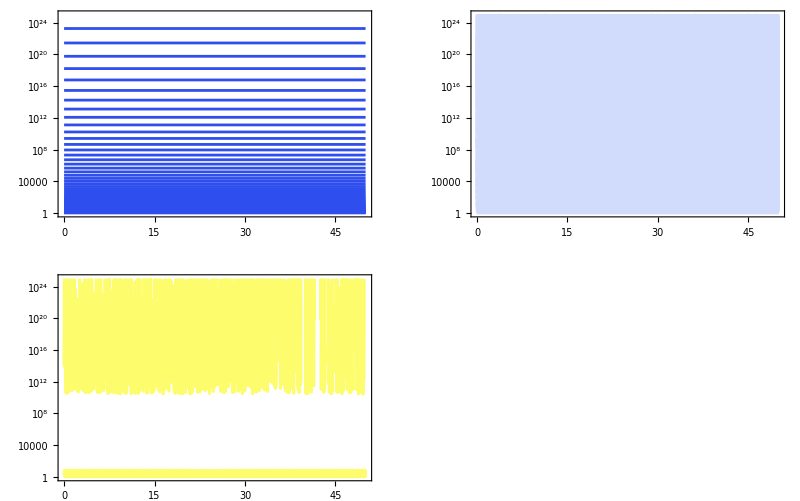
Sensitivity Analysis: Neural Evolution Robustness
-Graphics-

```mathematica
(*1. Define the Baseline Double Exponential*)baseRate=0.08;
tMax=50;
baseGrowth[t_]:=Exp[Exp[baseRate*t]-1];

(*2. Define a Perturbed Growth Function with'Noise'*)
(*This adds a random fluctuation (σ) to the growth rate*)
perturbedGrowth[t_,σ_]:=Exp[Exp[(baseRate+RandomReal[{-1,1}*σ])*t]-1];

(*3. Run Simulations across multiple'Noise' levels*)
noiseLevels={0.0,0.005,0.01,0.015};
simulations=Table[{Style["Noise: "<>ToString[n],12],LogPlot[Table[perturbedGrowth[t,n],{t,0,tMax}],{t,0,tMax},PlotRange->{1,10^25},PlotStyle->ColorData["TemperatureMap"][n/Max[noiseLevels]],Frame->True,Axes->False]},{n,noiseLevels}];

(*4. Visualize the Stability of the Complexity Gap*)
Column[{Style["Sensitivity Analysis: Neural Evolution Robustness",16,Bold],GraphicsGrid[Partition[simulations[[All,2]],2],ImageSize->800]}]
```

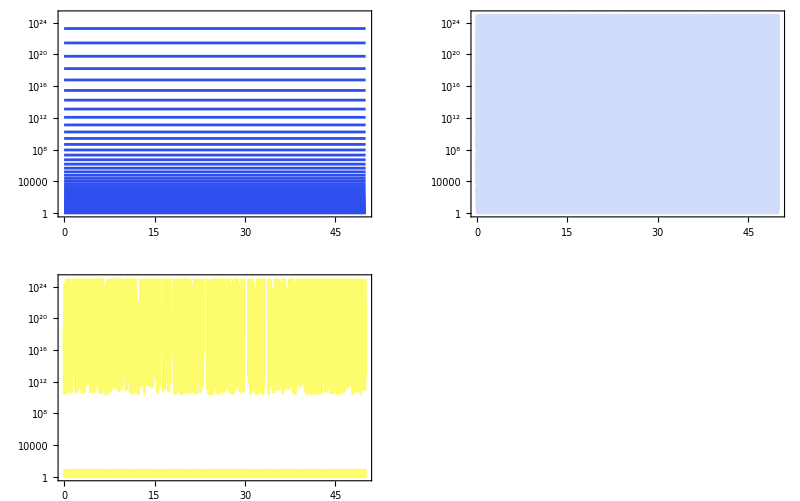
Sensitivity Analysis: Neural Evolution Robustness
-Graphics-

```mathematica
(*1. Define the Baseline Double Exponential*)baseRate=0.08;
tMax=50;
baseGrowth[t_]:=Exp[Exp[baseRate*t]-1];

(*2. Define a Perturbed Growth Function with'Noise'*)
(*This adds a random fluctuation (σ) to the growth rate*)
perturbedGrowth[t_,σ_]:=Exp[Exp[(baseRate+RandomReal[{-1,1}*σ])*t]-1];

(*3. Run Simulations across multiple'Noise' levels*)
noiseLevels={0.0,0.005,0.01,0.015};
simulations=Table[{Style["Noise: "<>ToString[n],12],LogPlot[Table[perturbedGrowth[t,n],{t,0,tMax}],{t,0,tMax},PlotRange->{1,10^25},PlotStyle->ColorData["TemperatureMap"][n/Max[noiseLevels]],Frame->True,Axes->False]},{n,noiseLevels}];

(*4. Visualize the Stability of the Complexity Gap*)
Column[{Style["Sensitivity Analysis: Neural Evolution Robustness",16,Bold],GraphicsGrid[Partition[simulations[[All,2]],2],ImageSize->800]}]
```

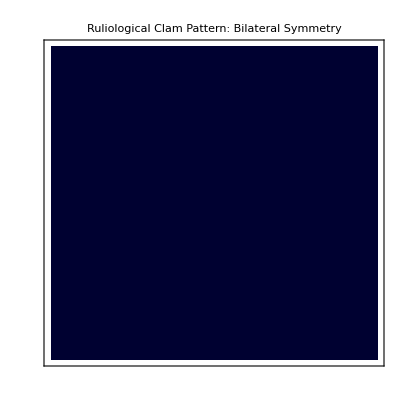

```mathematica
(*1. Setup Clam Geometry:Dense Symmetric Seed*)size=150;
hinge=75;
(*Create a 10x10 dense random cluster at the hinge*)
seedData=RandomInteger[1,{10,10}];
mirroredSeed=Join[Reverse[seedData,2],seedData,2];
initialSeed=CenterArray[mirroredSeed,{size,size}];

(*2. Run the'Healer' Rule 224-Increase steps to 150*)
rule={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
clamEvolution=CellularAutomaton[rule,initialSeed,150];

(*3. Visualization with higher contrast*)
ArrayPlot[Last[clamEvolution],ColorFunction->"RustTones",PlotLabel->Style["Ruliological Clam Pattern: Recovered Texture",14,Bold],Frame->True,Mesh->False]
```